# Cuaderno de prácticas de Matemática Discreta

## Práctica 2

## Grado en Ingeniería Informática Curso 2023/2024

## Datos personales :

Apellidos y nombre: Carrasco Vico, Juan
	DNI: 11111111 0
	Fecha de nacimiento: 25/03/2005
	Grupo de teoría: A
	Grupo de prácticas: 1

## Ejercicio 2.1:Calcular con 5 y 10 cifras significativas

### a)3 (1+4) - (2^5) 5 - 5^(1/5)

```mathematica
N[3 (1+4)-(2^5) 5-5^(1/5),5]
```

-146.38

```mathematica
N[3 (1+4)-(2^5) 5-5^(1/5),10]
```

-146.3797297

### b) 1/2 + 1/3 + 1/5

```mathematica
N[1/2 + 1/3+1/5,5]
```

1.0333

```mathematica
N[1/2 + 1/3+1/5,10]
```

1.033333333

### c)√5/3^(1/3)

```mathematica
N[√5/3^(1/3),5]
```

1.5504

```mathematica
N[√5/3^(1/3),10]
```

1.550402942

### d) ⅇ^2

```mathematica
N[ⅇ^2,5]
```

7.3891

```mathematica
N[ⅇ^2,10]
```

7.389056099

### e)Log[Cos[π/3]]

```mathematica
N[Log[Cos[π/3]],5]
```

-0.69315

```mathematica
N[Log[Cos[π/3]],10]
```

-0.6931471806

### f)Abs[1/2 + 1/3 -√2]

```mathematica
N[Abs[1/2+1/3-√2],5]
```

0.58088

```mathematica
N[Abs[1/2+1/3-√2], 10]
```

0.580880229

### g)Sin[π] + Tan [π]

```mathematica
N[Sin[π]+Tan[π],5]
```

0

```mathematica
N[Sin[π]+Tan[π],10]
```

0

### h)ArcSin[0.5] - ArcCos[0.5]

```mathematica
N[ArcSin[0.5]-ArcCos[0.5],5]
```

-0.523599

```mathematica
N[ArcSin[0.5]-ArcCos[0.5],10]
```

-0.523599

### i)2^1000

```mathematica
N[2^1000,5]
```

1.0715×10^301

```mathematica
N[2^1000,10]
```

1.071508607×10^301

## Ejercicio 2.4:Comprobar si son verdaderas o falsas las siguientes afirmaciones

### a) 3^50-2^50>(3-2)^50

```mathematica
3^50-2^50>(3-2)^50
```

True

### b) (Sin^2)[π/3]-Cos^2[π/3]<1

```mathematica
Sin[π/3] Sin[π/3]-Cos[π/3] Cos[π/3]<1
```

True

### c) √2+√3<= √(5□)

```mathematica
√2+√3<= √5
```

False

### d) PrimeQ[1001003]

```mathematica
PrimeQ[1001003]
```

True

### e) IntegerQ[1/2+3/10+1/5]

```mathematica
IntegerQ[1/2+3/10+1/5]
```

True

### f) N[(3/2)^2,1]>= 7/2

```mathematica
N[(3/2)^2,1]>= 7/2
```

False

### g)√Abs[2^15-3^15]>= √Abs[(2-3)^15]

```mathematica
√Abs[2^15-3^15]>= √Abs[(2-3)^15]
```

True

## Ejercicio 3.4:

### a)Vector cuyos coeficientes sean los números menores que 100 y múltiplos de 13

```mathematica
vector = Table[i,{i,0,100,13}]
```

{0,13,26,39,52,65,78,91}

### b) Vector que contenga los cuadrados de los múltiplos de 13 y menores que tu año de nacimiento al cuadrado

```mathematica
vector = Table[i^2,{i,1,2005,13}]
```

{1,196,729,1600,2809,4356,6241,8464,11025,13924,17161,20736,24649,28900,33489,38416,43681,49284,55225,61504,68121,75076,82369,90000,97969,106276,114921,123904,133225,142884,152881,163216,173889,184900,196249,207936,219961,232324,245025,258064,271441,285156,299209,313600,328329,343396,358801,374544,390625,407044,423801,440896,458329,476100,494209,512656,531441,550564,570025,589824,609961,630436,651249,672400,693889,715716,737881,760384,783225,806404,829921,853776,877969,902500,927369,952576,978121,1004004,1030225,1056784,1083681,1110916,1138489,1166400,1194649,1223236,1252161,1281424,1311025,1340964,1371241,1401856,1432809,1464100,1495729,1527696,1560001,1592644,1625625,1658944,1692601,1726596,1760929,1795600,1830609,1865956,1901641,1937664,1974025,2010724,2047761,2085136,2122849,2160900,2199289,2238016,2277081,2316484,2356225,2396304,2436721,2477476,2518569,2560000,2601769,2643876,2686321,2729104,2772225,2815684,2859481,2903616,2948089,2992900,3038049,3083536,3129361,3175524,3222025,3268864,3316041,3363556,3411409,3459600,3508129,3556996,3606201,3655744,3705625,3755844,3806401,3857296,3908529,3960100,4012009}

### c) Tabla de dos filas cuya primera fila sean los números impares comprendidos entre 20 y 36 y la segunda el resultado de sumar a la fila anterior tu número de nacimiento.

```mathematica
TableForm[Table[i*(25032005)^j,{j,0,1,1},{i,21,36,2}]]
```

21 | 23 | 25 | 27 | 29 | 31 | 33 | 35
525672105 | 575736115 | 625800125 | 675864135 | 725928145 | 775992155 | 826056165 | 876120175

### d) Crear una matriz 10x 10 tal que contenga un 1 en las componentes (i,j) tales que i+j es par y-1 en aquellas en las que i+j es impar.

```mathematica
matriz = Table[(-1)+2*(Mod[i+j,2]),{i,1,10,1}, {j,1,10,1}];MatrixForm[matriz]
```

(-1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1)

### e) Crear una tabla que simbolice un tablero de ajedrez de manera que en las casillas negras aparezca un 0 y en las casilla blancas aparezaca un 1

```mathematica
Table[Mod[i+j,2], {i,1,8,1},{j,1,8,1}]
```

{{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0}}

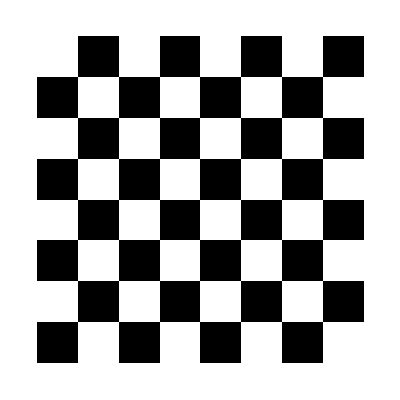

```mathematica
ArrayPlot[{{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0}}]
```